```mathematica
ClearAll["Global`*"]
SetDirectory[NotebookDirectory[]];
```

```mathematica
data=Import["/Users/vid/Documents/FS-MAG/5. Magisterij/Projektni Praktikum/log2grad/Log2F/Grad_0_PHANTOM.json","RawJSON"];
```

```mathematica
Keys[data]
```

{0,1,2,3,4,5,6,7,8,9,10}

```mathematica
data[["0"]][["1"]][["1"]][["F"]]
data[["2"]][["1"]][["1"]][["F"]]
data[["3"]][["1"]][["1"]][["F"]]
```

{1,0,0,1,1}

{1.2,4.87601×10^-36,3.46945×10^-18,0.913177,0.912565}

{1.3,5.30471×10^-36,6.93889×10^-18,0.877445,0.876671}

```mathematica
xcoords = Table[0,{i, Length[Keys[data]]}];
ycoords = xcoords;
frames = xcoords;
```

```mathematica
For[i=1, i <= 10, i++,
	frame = i;
	xcoords[[i]] = data[[ToString[i]]][["1"]][["1"]][["x"]];
	ycoords[[i]] = data[[ToString[i]]][["1"]][["1"]][["y"]];
	frames[[i]] = i;
	(*Print[data[[i]][["5"]][["1"]][["F"]]];*)
	
]
```

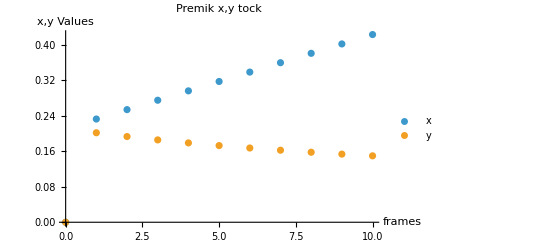

```mathematica
tockex = Transpose[{frames,xcoords}];
tockey =  Transpose[{frames,ycoords}];
ListPlot[{tockex, tockey}, PlotLabel->"Premik x,y tock", PlotLegends->{"x","y"},AxesLabel->{"frames","x,y Values"}]
```